```mathematica
tauY=2.99 10^(-5);
beta0Y=4.510695;
beta1Yl=-0.0000475;
beta1Yr=beta1Yl+tauY;
beta2Yl=1.64×10^(-7);
beta2Yr=beta2Yl-1.57×10^(-7);
beta3Yl=3.04×10^(-10);
beta3Yr=beta3Yl-3.09×10^(-10);
beta4Yl=1.82×10^(-13);
beta4Yr=beta4Yl-1.81×10^(-13);
beta5Yl=3.53×10^(-17);
beta5Yr=beta5Yl-3.55×10^(-17);

tauB=2.3 10^(-5);
beta0B=3.169924;
beta1Bl=8.40×10^(-6);
beta1Br=beta1Bl+tauB;
beta2Bl=-1.21×10^(-8);
beta2Br=beta2Bl+1.74×10^(-8);
beta3Bl=-1.01×10^(-11);
beta3Br=beta3Bl+6.28×10^(-12);
beta4Bl=-7.56×10^(-16);
beta4Br=beta4Bl+1.71×10^(-15);
beta5Bl=7.89×10^(-19);
beta5Br=beta5Bl-8.69×10^(-19);

fYl[x_]:=beta0Y+beta1Yl x+beta2Yl x^2+beta3Yl x^3+beta4Yl x^4+beta5Yl x^5;
fYr[x_]:=beta0Y+beta1Yr x+beta2Yr x^2+beta3Yr x^3+beta4Yr x^4+beta5Yr x^5;

fBl[x_]:=beta0B+beta1Bl x+beta2Bl x^2+beta3Bl x^3+beta4Bl x^4+beta5Bl x^5;
fBr[x_]:=beta0B+beta1Br x+beta2Br x^2+beta3Br x^3+beta4Br x^4+beta5Br x^5;
```

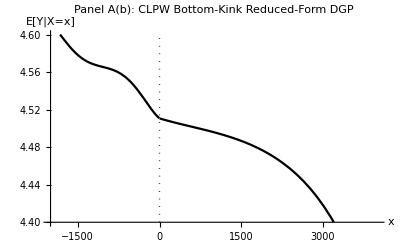

```mathematica
verticalY=Line[{{0,4.4},{0,4.6}}];
DGPBottomKinkY=Plot[Piecewise[{{fYl[x],x<0},{fYr[x],x>0}}],{x,-2000,4000},
	PlotStyle-> {Black},
	PlotLabel-> "Panel A(b): CLPW Bottom-Kink Reduced-Form DGP",
	BaseStyle-> {FontFamily-> "Times"},AxesLabel-> {"x","E[Y|X=x]"},
	AxesOrigin->{-2000,4.4},
	PlotRange->{{-2000,4000},{4.4,4.6}},
	Epilog->{Directive[Dotted],verticalY}]
Export["C:/Users/zp53/Dropbox/local poly/graphs/RKD DGP BottomKinkY.pdf",DGPBottomKinkY, ImageSize->Medium];
```

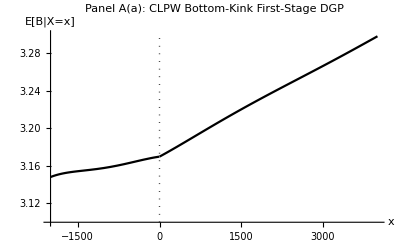

```mathematica
verticalB=Line[{{0,3.1},{0,3.3}}];
DGPBottomKinkB=Plot[Piecewise[{{fBl[x],x<0},{fBr[x],x>0}}],{x,-2000,4000},
	PlotStyle-> {Black},
	PlotLabel-> "Panel A(a): CLPW Bottom-Kink First-Stage DGP",
	BaseStyle-> {FontFamily-> "Times"},AxesLabel-> {"x","E[B|X=x]"},
	AxesOrigin->{-2000,3.1},
	PlotRange->{{-2000,4000},{3.1,3.3}},
	Epilog->{Directive[Dotted],verticalB}]
Export["C:/Users/zp53/Dropbox/local poly/graphs/RKD DGP BottomKinkB.pdf",DGPBottomKinkB, ImageSize->Medium];
```